```mathematica
G11[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo-zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G22[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo+zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G12[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
Nulls[Jone_,Jtwo_,p_,z_]:=1-G11[1,Jone,Jtwo,p,z]-G22[1,Jone,Jtwo,p,z]-G12[1,Jone,Jtwo,p,z]^2+G11[1,Jone,Jtwo,p,z]G22[1,Jone,Jtwo,p,z]
```

```mathematica
Zero[J_,q_,u_] := √(J^4/(J^2+J u)+(J^3 u)/(J^2+J u)+(J^2 u^2)/(2 (J^2+J u))+(J u^3)/(8 (J^2+J u))-1/(8 (J^2+J u))(√(256 J^4 J q^2+512 J^3 J q^2 u+64 J^6 u^2+320 J^2 J q^2 u^2+96 J^5 u^3+64 J  J q^2 u^3+52 J^4 u^4+12 J^3 u^5+J^2 u^6)))
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_,Jone_,p_] := Module[{lst={{Xstart,FindRoot[Nulls[Jone,Xstart,p,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.005;
a=Check[FindRoot[Nulls[Jone,Jtwoo,p,z]==0,{z,z/.lst[[n,2]]}]
,z->0];
AppendTo[lst,{Jtwoo,a}];
,{n,1,19,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,20,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,20,1}];
lst
]
```

```mathematica
Verlauf[HowMany_,p_] := Module[{lst={}},
For[i=0,i<HowMany,i++,
AppendTo[lst,{1,i*0.1,p}];
AppendTo[lst,Fueger[moduler[Lister[-1,-0.005,Zero[1,i*0.1,2*p],i*0.1,p]],moduler[Lister[1,0.005,Zero[1,i*0.1,2*p],i*0.1,p]]]]
];
l = lst
]
```

```mathematica
Verlauf[3,-0.1]
```

{{1,0.,-0.1},{{-0.005,0.899865},{-0.01,0.899462},{-0.015,0.898793},{-0.02,0.89786},{-0.025,0.896668},{-0.03,0.895225},{-0.035,0.893535},{-0.04,0.891609},{-0.045,0.889453},{-0.05,0.887078},{-0.055,0.884492},{-0.06,0.881705},{-0.065,0.878726},{-0.07,0.875564},{-0.075,0.872229},{-0.08,0.868728},{-0.085,0.86507},{-0.09,0.861262},{-0.095,0.857312},{-0.1,0.853226},{0.005,0.899866},{0.01,0.899464},{0.015,0.898797},{0.02,0.897869},{0.025,0.896687},{0.03,0.895256},{0.035,0.893584},{0.04,0.89168},{0.045,0.889553},{0.05,0.887211},{0.055,0.884664},{0.06,0.881922},{0.065,0.878994},{0.07,0.875889},{0.075,0.872616},{0.08,0.869183},{0.085,0.865597},{0.09,0.861868},{0.095,0.858},{0.1,0.854001}},{1,0.1,-0.1},{{-0.005,0.851817},{-0.01,0.848837},{-0.015,0.845579},{-0.02,0.84206},{-0.025,0.838299},{-0.03,0.834313},{-0.035,0.83012},{-0.04,0.825734},{-0.045,0.821169},{-0.05,0.816439},{-0.055,0.811556},{-0.06,0.806529},{-0.065,0.801367},{-0.07,0.79608},{-0.075,0.790673},{-0.08,0.785153},{-0.085,0.779525},{-0.09,0.773793},{-0.095,0.767963},{-0.1,0.762036},{0.005,0.856869},{0.01,0.858909},{0.015,0.860607},{0.02,0.861953},{0.025,0.86294},{0.03,0.863566},{0.035,0.863831},{0.04,0.863741},{0.045,0.863302},{0.05,0.862525},{0.055,0.861425},{0.06,0.860014},{0.065,0.858309},{0.07,0.856325},{0.075,0.854078},{0.08,0.851584},{0.085,0.848859},{0.09,0.845917},{0.095,0.84277},{0.1,0.839432}},{1,0.2,-0.1},{{-0.005,0.748483},{-0.01,0.743114},{-0.015,0.737576},{-0.02,0.731879},{-0.025,0.726033},{-0.03,0.720046},{-0.035,0.713924},{-0.04,0.707673},{-0.045,0.701298},{-0.05,0.694803},{-0.055,0.68819},{-0.06,0.681461},{-0.065,0.67462},{-0.07,0.667666},{-0.075,0.660599},{-0.08,0.653421},{-0.085,0.646131},{-0.09,0.638728},{-0.095,0.63121},{-0.1,0.623576},{0.005,0.758665},{0.01,0.763448},{0.015,0.768003},{0.02,0.772313},{0.025,0.776357},{0.03,0.780115},{0.035,0.783565},{0.04,0.786687},{0.045,0.789461},{0.05,0.79187},{0.055,0.793898},{0.06,0.795536},{0.065,0.796776},{0.07,0.797616},{0.075,0.798058},{0.08,0.798109},{0.085,0.797779},{0.09,0.797081},{0.095,0.796031},{0.1,0.794646}}}

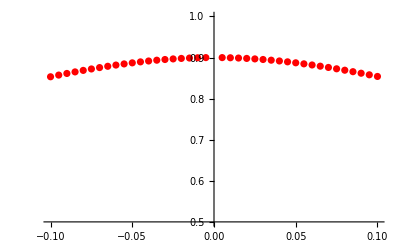

```mathematica
A = ListPlot[{{-0.005,0.899865486342821},{-0.01,0.8994624304483313},{-0.015,0.8987927300707611},{-0.02,0.8978597838164608},{-0.025,0.8966683777860729},{-0.03,0.8952245326893282},{-0.035,0.8935353220544772},{-0.04,0.8916086731702563},{-0.045,0.88945316217508},{-0.05,0.8870778134738458},{-0.055,0.884491911738461},{-0.06,0.8817048324895824},{-0.065,0.8787258949815372},{-0.07,0.87556423906084},{-0.075,0.8722287259794512},{-0.08,0.86872786189172},{-0.085,0.8650697419139568},{-0.09,0.8612620121599831},{-0.095,0.8573118469824297},{-0.1,0.8532259386882597},{0.005,0.8998656399912153},{0.01,0.8994636537963471},{0.015,0.8987968265064384},{0.02,0.8978693888132562},{0.025,0.8966868811759011},{0.03,0.8952559838794547},{0.035,0.8935843243111518},{0.04,0.8916802731308007},{0.045,0.8895527402177427},{0.05,0.8872109796327129},{0.055,0.8846644106868747},{0.06,0.8819224599016988},{0.065,0.8789944264623966},{0.07,0.8758893718873828},{0.075,0.8726160331727614},{0.08,0.8691827576385857},{0.085,0.8655974570557619},{0.09,0.861867578331839},{0.095,0.8580000879745328},{0.1,0.8540014676763447}},PlotStyle->{Red},PlotRange->{0.5,1}]
```

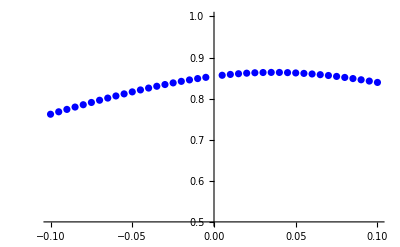

```mathematica
B = ListPlot[{{-0.005,0.851817021214664},{-0.01,0.8488372997456295},{-0.015,0.8455788532760256},{-0.02,0.8420600465393536},{-0.025,0.8382990565930841},{-0.03,0.8343134421054639},{-0.035,0.8301198271341518},{-0.04,0.8257336909812681},{-0.045,0.8211692487208532},{-0.05,0.816439404137469},{-0.055,0.8115557569346296},{-0.06,0.8065286479886997},{-0.065,0.8013672291799866},{-0.07,0.7960795472625412},{-0.075,0.7906726339386496},{-0.08,0.7851525966034867},{-0.085,0.7795247060577173},{-0.09,0.7737934788817714},{-0.095,0.7679627531841818},{-0.1,0.7620357571513292},{0.005,0.8568692341781415},{0.01,0.8589093531704772},{0.015,0.8606073725318385},{0.02,0.8619532730957528},{0.025,0.8629404859227445},{0.03,0.8635661785075325},{0.035,0.8638313182322822},{0.04,0.8637405121390841},{0.045,0.8633016514146582},{0.05,0.8625254108557843},{0.055,0.8614246641766539},{0.06,0.8600138750800655},{0.065,0.8583085143122512},{0.07,0.8563245384271406},{0.075,0.8540779508668574},{0.08,0.8515844524689898},{0.085,0.8488591789933743},{0.09,0.8459165167027465},{0.095,0.8427699840064636},{0.1,0.8394321663097011}},PlotStyle->{Blue},PlotRange->{0.5,1}]
```

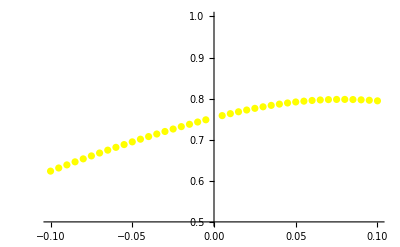

```mathematica
DD = ListPlot[{{-0.005,0.7484834098231707},{-0.01,0.7431140795450425},{-0.015,0.7375757378693601},{-0.02,0.7318790089540628},{-0.025,0.7260330935826821},{-0.03,0.7200458852984055},{-0.035,0.7139240888131906},{-0.04,0.7076733346013035},{-0.045,0.701298285933513},{-0.05,0.6948027362988493},{-0.055,0.6881896963223565},{-0.06,0.6814614700458248},{-0.065,0.6746197209042067},{-0.07,0.6676655280468112},{-0.075,0.6605994333068429},{-0.08,0.6534214807725982},{-0.085,0.6461312476330291},{-0.09,0.6387278689614306},{-0.095,0.6312100557660517},{-0.1,0.6235761071573053},{0.005,0.758664819246358},{0.01,0.7634477314478979},{0.015,0.7680032863802935},{0.02,0.7723129532088566},{0.025,0.7763569302391824},{0.03,0.7801145197103546},{0.035,0.7835646592496984},{0.04,0.7866866080425511},{0.045,0.7894607612579949},{0.05,0.7918695375424517},{0.055,0.7938982578891333},{0.06,0.79553591832393},{0.065,0.7967757610431646},{0.07,0.7976155717130281},{0.075,0.7980576705282044},{0.08,0.7981086111893011},{0.085,0.797778642880953},{0.09,0.797081016013443},{0.095,0.796031219300202},{0.1,0.794646226161407}},PlotStyle->{Yellow},PlotRange->{0.5,1}]
```

```mathematica
"1,0.`,-0.1`","1,0.1`,-0.1`","1,0.2`,-0.1`"
```

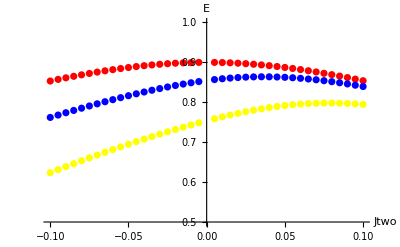

```mathematica
Show[A,B,DD,AxesLabel->{Jtwo,"E"},PlotLegends->{"a","b","c"}]
```

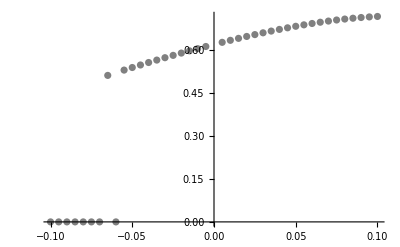

```mathematica
ListPlot[{{-0.005,0.6117648836498478},{-0.01,0.6042637409721414},{-0.015,0.5966026540604186},{-0.02,0.5887825085752489},{-0.025,0.5808032206205652},{-0.03,0.572663788701482},{-0.035,0.564362330538969},{-0.04,0.5558961050598283},{-0.045,0.5472615197468418},{-0.05,0.5384541232958237},{-0.055,0.5294685832039057},{-0.06,0},{-0.065,0.5109370893947955},{-0.07,0},{-0.075,0},{-0.08,0},{-0.085,0},{-0.09,0},{-0.095,0},{-0.1,0},{0.005,0.6262785258217773},{0.01,0.6332837220047149},{0.015,0.6401141570055011},{0.02,0.6467627860991892},{0.025,0.6532209808938041},{0.03,0.6594784006867233},{0.035,0.6655228769841898},{0.04,0.6713403280961968},{0.045,0.6769147265087113},{0.05,0.6822281474738502},{0.055,0.6872609315258956},{0.06,0.6919919942114043},{0.065,0.6963993104477042},{0.07,0.7004605859469528},{0.075,0.7041541028957232},{0.08,0.7074596935061754},{0.085,0.7103597594455223},{0.09,0.7128402275993928},{0.095,0.7148913240385603},{0.1,0.716508065244887}},PlotStyle->Gray]
```